```mathematica
(*Code created by Loïc Marrec*)
```

```mathematica
(*Description: Fixation probabilities in the island and stepping stone models*)
```

```mathematica
(*PARAMETERS*)
```

```mathematica
bW=1;(*Wild-type birth rate*)
```

```mathematica
dW=0.1;(*Wild-type death rate*)
```

```mathematica
bM=Table[i,{i,0.95,1.1,0.001}];(*Mutant birth rates*)
```

```mathematica
dM=0.1;(*Mutant death rate*)
```

```mathematica
Δ=5;(*Number of demes*)
```

```mathematica
κ=100;(*Carrying capacity*)
```

```mathematica
(*EQULIBRIUM DEME SIZES*)
```

```mathematica
NW=κ (1-dW/bW);(*Wild-type deme equilibrium size*)
```

```mathematica
NM=Table[κ (1-dM/bM[[i]]),{i,Length[bM]}];(*Mutant deme equilibrium sizes*)
```

```mathematica
(*FIXATION PROBABILITIES WITHIN DEMES*)
```

```mathematica
uW=Table[If[bM[[i]]==bW*dM/dW,1/NM[[i]],(1-(bM[[i]]*dW)/(bW*dM))/(1-((bM[[i]]*dW)/(bW*dM))^NM[[i]])],{i,Length[bM]}]; (*Fixation probability of a wild type in a mutant deme*)
```

```mathematica
uM=Table[If[bM[[i]]==bW*dM/dW,1/NW,(1-(bW*dM)/(bM[[i]]*dW))/(1-((bW*dM)/(bM[[i]]*dW))^NW)],{i,Length[bM]}]; (*Fixation probability of a mutant in a wild-type deme*)
```

```mathematica
(*DISPERSAL RATIOS*)
```

```mathematica
α={1/5,1/2,1,2,5};
```

```mathematica
(*RELATIVE FITNESS OF MUTANT DEMES*)
```

```mathematica
r=Table[α[[j]]*(NM[[i]]*uM[[i]])/(NW*uW[[i]]),{i,Length[bM]},{j,Length[α]}];
```

```mathematica
(*GLOBAL FIXATION PROBABILITIES*)
```

```mathematica
U=Table[If[r[[i,j]]==1,1/Δ,(1-r[[i,j]]^-1)/(1-r[[i,j]]^-Δ)],{i,Length[bM]},{j,Length[α]}];
```

```mathematica
(*DATA TABLES FOR PLOTTING*)
```

```mathematica
Utable=Table[{bM[[j]]/bW-1,U[[j,i]]},{i,Length[α]},{j,Length[bM]}]; (*Single-deme fixation probability*)
```

```mathematica
utable=Table[{bM[[j]]/bW-1,uM[[j]]*U[[j,i]]},{i,Length[α]},{j,Length[bM]}]; (*Single-individual fixation probability*)
```

```mathematica
(*PLOTTING*)
```

```mathematica
colorRain=Table[ColorData["Rainbow"][k],{k,0,1,1/(Length[α]-1)}];
```

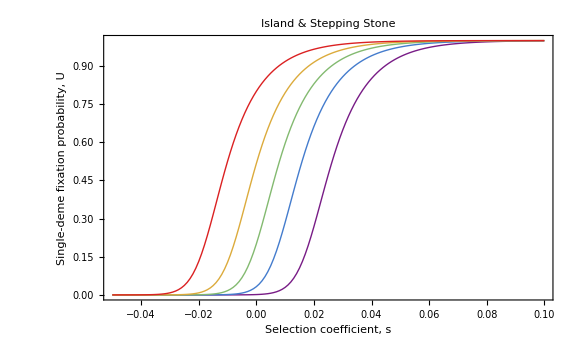

```mathematica
Show[Table[ListPlot[Utable[[f]],PlotStyle->{colorRain[[f]],Thick},Joined->True],{f,Length[α]}],PlotLabel->"Island & Stepping Stone",PlotRange->All,AxesLabel->{"Selection coefficient, s","Global fixation probability, U"},Frame->True,FrameLabel->{"Selection coefficient, s","Single-deme fixation probability, U"},ImageSize->Large]
```